Equivariant Verlinde Formula from Superconformal Index and Argyres-Seiberg duality

#### S. Gukov, D. Pei, W. Yan and K. Ye

In this Mathematica notebook we provide calculation of Coulomb branch Index on Lens spaces of class S theories. In section 1 we demonstrate the equivalence of the index with equivariant Verlinde formula for SU(2) gauge group. In section 2 we use Argyres-Seiberg duality to compute the equivariant Verlinde formula for SU(3) and show some properties of the moduli space of rank 3 Higgs bundle.

## 1. SU(2) Case

```mathematica
Quit[]
```

Here we compute Lens space index of A_1class S theory. We begin by listing the single particle index and its Coulomb branch limit, then we calculate the plethystic exponential explicitly.

#### 1.1 Single particle index

```mathematica
SingleTrif[τ_,ρ_,η_,m_,r_]:=((τ η)^m/(1-(τ η)^r)+(τ ρ)^(r-m)/(1-(τ ρ)^r))/(1-τ^2 ρ η)(τ-τ ρ η);
```

```mathematica
SingleVect[τ_,ρ_,η_,m_,r_]:=((τ η)^m/(1-(τ η)^r)+(τ ρ)^(r-m)/(1-(τ ρ)^r))/(1-τ^2 ρ η)(τ^2 ρ η+ρ η-1-τ^2)+KroneckerDelta[m,0];
```

```mathematica
ZeroTrif[τ_,ρ_,η_,m1_,m2_,m3_,r_]:=(ρ η)^(1/4 Sum[Mod[m1 s1+m2 s2+m3 s3,r]-1/r(Mod[m1 s1+m2 s2+m3 s3,r])^2,{s1,-1,1,2},{s2,-1,1,2},{s3,-1,1,2}]);
```

```mathematica
ZeroVect[τ_,ρ_,η_,m_,r_]:=(ρ η)^(-Mod[2m,r]+1/r(Mod[2m,r])^2);
```

#### 1.2 Coulomb branch index

```mathematica
rsum[r2_]:=r2/2;
```

The Dirac quantization condition is encoded in the zero point energy of trifundamentals:

```mathematica
ℐH2[m1_,m2_,m3_,r2_]:=If[IntegerQ[m1+m2+m3],ZeroTrif[0,ρ,η,m1,m2,m3,r2],0];
```

```mathematica
ℐV2[m_,r2_]:=ZeroVect[0,ρ,η,m,r2] (1/(1-ρ η))(1/(1+ρ η))^KroneckerDelta[Mod[2m,r2],0];
```

The following two formulas are for Riemann surface of genus 2 and 3.

```mathematica
SindexLensG2[r2_]:=Sum[ℐH2[m1,m1,m2,r2]ℐV2[m1,r2]ℐV2[m2,r2]ℐV2[m3,r2]ℐH2[m2,m3,m3,r2],{m1,0,rsum[r2],1/2},{m2,0,rsum[r2],1/2},{m3,0,rsum[r2],1/2}]/.η->t/ρ;
```

```mathematica
SindexLensG3[r2_]:=Sum[ℐV2[m1,r2]ℐH2[m1,m1,m2,r2]ℐV2[m2,r2]ℐH2[m2,m3,m4,r2]ℐV2[m3,r2]ℐV2[m4,r2]ℐH2[m3,m4,m5,r2]ℐV2[m5,r2]ℐH2[m5,m6,m6,r2]ℐV2[m6,r2],{m1,0,rsum[r2],1/2},{m2,0,rsum[r2],1/2},{m3,0,rsum[r2],1/2},{m4,0,rsum[r2],1/2},{m5,0,rsum[r2],1/2},{m6,0,rsum[r2],1/2}]/.η->t/ρ;
```

The next two expressions are for crossing symmetry of the four punctured sphere. This is the demonstration that the TQFT algebra is associative.

```mathematica
CBIalg[k_]:=Table[ℐH2[m1,m2,m3,k]ℐV2[m3,k](ZeroVect[0,ρ,η,m1,k]ZeroVect[0,ρ,η,m2,k])^(1/2)ZeroVect[0,ρ,η,m3,k]^(-1/2),{m1,0,rsum[k],1/2},{m2,0,rsum[k],1/2},{m3,0,rsum[k],1/2}];
```

```mathematica
CheckAss[m1_,m2_,n1_,n2_,k_]:=Sum[ℐH2[m1,m2,m,k]ℐV2[m,k]ℐH2[m,n1,n2,k]-ℐH2[m1,n1,m,k]ℐV2[m,k]ℐH2[m,m2,n2,k],{m,0,rsum[k],1/2}]
```

```mathematica
CheckAss[1/2,3/2,0,1,4]//Simplify
```

0

#### 1.3 EVA from Hitchin moduli space

We perform the computation by equivariant integration over Hithin moduli space, and use cutting and gluing to get the general partition function on genus g Riemann surfaces.

eta (η) is the metric for the TQFT, and f is the structure constant associated to three punctured sphere.

```mathematica
eta[k_]:={(1-t^2)^-1}~Join~Table[(1-t)^-1,{i,1,k-1}]~Join~{(1-t^2)^-1};
```

```mathematica
d0[λ1_,λ2_,λ3_,k_]:=λ1+λ2+λ3-2k;
d1[λ1_,λ2_,λ3_]:=λ1-λ2-λ3;
d2[λ1_,λ2_,λ3_]:=λ2-λ3-λ1;
d3[λ1_,λ2_,λ3_]:=λ3-λ1-λ2;
```

```mathematica
Δλ[λ1_,λ2_,λ3_,k_]:=Max[d0[λ1,λ2,λ3,k],d1[λ1,λ2,λ3],d2[λ1,λ2,λ3],d3[λ1,λ2,λ3]];
```

```mathematica
f[λ1_,λ2_,λ3_,k_]:=Which[
EvenQ[λ1+λ2+λ3]&&Δλ[λ1,λ2,λ3,k]≤0,1,
EvenQ[λ1+λ2+λ3]&&Δλ[λ1,λ2,λ3,k]>0,t^(Δλ[λ1,λ2,λ3,k]/2),
OddQ[λ1+λ2+λ3],0];
```

```mathematica
Fppants[k_]:=Table[f[λ1,λ2,λ3,k],{λ1,0,k},{λ2,0,k},{λ3,0,k}];
```

The partition function on genus 2 and 3 Riemann surfaces are

```mathematica
CutGlue2[k_]:=Sum[Fppants[k]⟦λ1,λ2,λ3⟧Fppants[k]⟦λ1,λ2,λ3⟧eta[k]⟦λ1⟧eta[k]⟦λ2⟧eta[k]⟦λ3⟧,{λ1,1,k+1},{λ2,1,k+1},{λ3,1,k+1}];
```

```mathematica
CutGlue3[k_]:=Sum[eta[k]⟦λ1⟧Fppants[k]⟦λ1,λ1,λ2⟧eta[k]⟦λ2⟧Fppants[k]⟦λ2,λ3,λ4⟧eta[k]⟦λ3⟧eta[k]⟦λ4⟧Fppants[k]⟦λ3,λ4,λ5⟧eta[k]⟦λ5⟧Fppants[k]⟦λ5,λ6,λ6⟧eta[k]⟦λ6⟧,{λ1,1,k+1},{λ2,1,k+1},{λ3,1,k+1},{λ4,1,k+1},{λ5,1,k+1},{λ6,1,k+1}];
```

The following definition is we use metric to raise one index. Such pair of pants contribution is useful to understand the TQFT algebra.

```mathematica
VAF[k_]:=Table[f[m1,m2,m3-1,k]eta[k]⟦m3⟧,{m1,0,k},{m2,0,k},{m3,1,k+1}];
```

#### 1.4 Examples (Partition function)

We show here that the index is equal to the partition function.

```mathematica
{SindexLensG2[1],CutGlue2[1]}//Simplify
```

{-4/((-1+t^2)^3),-4/((-1+t^2)^3)}

```mathematica
{SindexLensG2[2],CutGlue2[2]}//Simplify
```

{-(2 (5+6 t+5 t^2))/((-1+t^2)^3),-(2 (5+6 t+5 t^2))/((-1+t^2)^3)}

```mathematica
{SindexLensG2[3],CutGlue2[3]}//Simplify
```

{-(4 (5+9 t+9 t^2+4 t^3))/((-1+t^2)^3),-(4 (5+9 t+9 t^2+4 t^3))/((-1+t^2)^3)}

```mathematica
{SindexLensG2[4],CutGlue2[4]}//Simplify
```

{-(35+75 t+81 t^2+49 t^3+16 t^4)/((-1+t^2)^3),-(35+75 t+81 t^2+49 t^3+16 t^4)/((-1+t^2)^3)}

```mathematica
{SindexLensG3[1],CutGlue3[1]}//Simplify
```

{8/((-1+t^2)^6),8/((-1+t^2)^6)}

```mathematica
{SindexLensG3[2],CutGlue3[2]}//Simplify
```

{(4 (9+28 t+54 t^2+28 t^3+9 t^4))/((-1+t^2)^6),(4 (9+28 t+54 t^2+28 t^3+9 t^4))/((-1+t^2)^6)}

```mathematica
{SindexLensG3[3],CutGlue3[3]}//Simplify
```

{(8 (15+72 t+183 t^2+238 t^3+159 t^4+54 t^5+8 t^6))/((-1+t^2)^6),(8 (15+72 t+183 t^2+238 t^3+159 t^4+54 t^5+8 t^6))/((-1+t^2)^6)}

## 2. E_6 SCFT

Having demonstrated that the superconformal index is the same as equivariant Verlinde formula in the case of SU(2), we now assume this equivalence and proceed to compute the equivariant Verlinde formula for moduli space of rank 3 Higgs bundle. The Riemann surface is three maximally punctured sphere, and the 4d N=2 theory is the E_6SCFT, or T_3 theory. The index can be inferred by Argyres-Seiberg duality.

#### 2.1 Holonomy choice

To begin with let us fix the holonomy choices for each flavor symmetry. For T_3 theory the three maximal puncture has (h_1^a, h_2^a, h_3^a). The total sum of holonomy should be integer, which fixes the h^avalue to be
(0,0,0),  (1/3,1/3,-2/3), (2/3,2/3,-1/3)
Moreover, the three punctures either all choose same set of holonomy (e.g. their numerator are all equal to 1 mod 3), or each chooses different set of holonomy (the numerator has distinct remainders modulo 3). When gauging one SU(3) flavor symmetry, we make change of variables:
 (h_1^c, h_2^c,h_3^c) → (v+w,v-w,-2v)
 Then by the definition of h's, we see w takes value in ℤ/2, and v takes value in ℤ/2 ± 1/3. Moreover, since 2 and 3 are coprime, if w is half-odd, v must be half-odd plus/minus 1/3.
 There is also one more flavor symmetry U(1) acting on the single hypermultiplet in the dual frame, n_s. In the dual frame, the total holonomy should be integer. Therefore, n_s takes value in ℤ/2 as well. Moreover we can fix the number of possible values of n_s equal to the number of possible values of w.
 Finally, the two U(1) charges, n_a and n_bin the original, weakly interacting frame is given by similar change of variables:
 n_a=1/3 n_s-v,      n_b=-1/3 n_s-v 
 In this convention one can also check in the weakly coupled frame the total holonomy is also integer, so the Dirac quantization condition is satisfied.

We further define the fundamental domain of holonomy to be 
h_1≥h_2, h_1≥-2 h_2, 2 h_1+h_2≤k.

```mathematica
LowLim[x_]:=If[IntegerQ[(3x)/2],-x/2,x-Floor[3 x/2]];
```

```mathematica
Fdomain[k_]:=Table[{h1,h2,-h1-h2},{h1,0,(2k)/3,1/3},{h2,LowLim[h1],Min[h1,k-2h1],1}];
```

```mathematica
FdomainPlot[k_]:=Plot[{h1,-h1/2,k-2h1},{h1,0,2k/3},PlotStyle->Thick]
```

```mathematica
F3=ListPlot[Table[Flatten[Fdomain[3],1]⟦i⟧//Drop[#,-1]&,{i,1,Length[Flatten[Fdomain[3],1]]}],PlotStyle->{Red},PlotMarkers->{"●",Medium}];
```

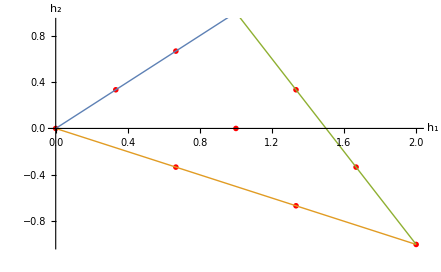

```mathematica
F3e=Show[F3,FdomainPlot[3],PlotRange->{-1,0.91},AxesLabel->{Subscript[h, 1],Subscript[h, 2]}]
```

#### 2.2 Index for SU(3) theory with 6 flavors

We now compute the weakly coupled Lagrangian description of the dual theories. SU(3) gauge theory with 6 flavors of hypermultiplets is superconformal, and the Coulomb branch index comes from vectors and zero point energy of hypermultiplets.

```mathematica
SU3Vec[m1_,m2_,m3_,k_]:=If[m1==m2||m1-m2==k,If[m2==m3||m2-m3==k,1/((1-t^2)(1-t^3)),1/((1-t)(1-t^2))],If[m1==m3||m1-m3==k,1/((1-t)(1-t^2)),If[m2==m3||m2-m3==k,1/((1-t)(1-t^2)),1/(1-t)^2]]];
```

```mathematica
ZV3[m1_,m2_,m3_,k_]:=t^(-Mod[m1-m2,k]+1/k(Mod[m1-m2,k])^2-Mod[m1-m3,k]+1/k(Mod[m1-m3,k])^2-Mod[m2-m3,k]+1/k(Mod[m2-m3,k])^2);
```

```mathematica
ZH3[m_,n_,a_,k_]:=t^(1/2(Mod[m+n+a,k]-1/k Mod[m+n+a,k]^2));
```

During computation one needs to worry that if the holonomy we choose lies in the fundamental domain we defined above. If it is not, we need to transform them into the fundamental domain.

```mathematica
Punc3[a_,b_]:=If[IntegerQ[a-b],a-Floor[a],-a-b-Floor[-a-b]];
```

```mathematica
InDomain[a1_,a2_,k_]:=If[IntegerQ[a1-a2]&&a2≥-a1/2&&a2≤a1&&a2≤k-2a1,True,False];
```

Then the total index for SU(3) with six hypermultiplets is:

```mathematica
S3N6[a1_,a2_,b1_,b2_,ny_,ns_,k_]:=
If[IntegerQ[3(ny+ns)]&&InDomain[a1,a2,k]&&InDomain[b1,b2,k]&&IntegerQ[-2ny-Punc3[a1,b1]],Sum[SU3Vec[m1,m2,-m1-m2,k]ZV3[m1,m2,-m1-m2,k](ZH3[m1,a1,1/3 ns-ny,k]ZH3[m2,a1,1/3 ns-ny,k]ZH3[-m1-m2,a1,1/3 ns-ny,k]ZH3[m1,a2,1/3 ns-ny,k]ZH3[m2,a2,1/3 ns-ny,k]ZH3[-m1-m2,a2,1/3 ns-ny,k]ZH3[m1,-a1-a2,1/3 ns-ny,k]ZH3[m2,-a1-a2,1/3 ns-ny,k]ZH3[-m1-m2,-a1-a2,1/3 ns-ny,k]ZH3[-m1,b1,-1/3 ns-ny,k]ZH3[-m2,b1,-1/3 ns-ny,k]ZH3[m1+m2,b1,-1/3 ns-ny,k]ZH3[-m1,b2,-1/3 ns-ny,k]ZH3[-m2,b2,-1/3 ns-ny,k]ZH3[m1+m2,b2,-1/3 ns-ny,k]ZH3[-m1,-b1-b2,-1/3 ns-ny,k]ZH3[-m2,-b1-b2,-1/3 ns-ny,k]ZH3[m1+m2,-b1-b2,-1/3 ns-ny,k]),{m1,Punc3[a1,1/3 ns-ny],2k/3},{m2,LowLim[m1],Min[m1,k-2m1]}],0];
```

#### 2.3 Inversion and E_6 index

Now we turn to the dual description of the theory, which is the gauging SU(2) subgroup with a single hypermultiplet of an isolated SCFT (T_3 theory). We need to separate the contribution of this theory. We first define the index for the single hypermultiplet:

```mathematica
IH2[k_]:=Table[If[IntegerQ[w+ns],t^(1/2(Mod[w+ns,k]-(Mod[w+ns,k])^2/k))t^(1/2(Mod[-w+ns,k]-(Mod[-w+ns,k])^2/k)),0],{w,0,k/2,1/2},{ns,0,k/2,1/2}];
```

For large k→∞, the above expression can be simplified:

```mathematica
IH2Asym[k_]:=Table[If[IntegerQ[w+ns],t^(1/2(w+ns))t^(1/2 Abs[-w+ns]),0],{w,0,k/2,1/2},{ns,0,k/2,1/2}];
```

```mathematica
IHinv[k_]:=Inverse[IH2[k]];
```

```mathematica
E6SCFT[a1_,a2_,b1_,b2_,c1_,c2_,k_]:=If[InDomain[a1,a2,k]&&InDomain[b1,b2,k]&&InDomain[c1,c2,k],1/ℐV2[(c1-c2)/2,k] Sum[S3N6[a1,a2,b1,b2,(c1+c2)/2,ns,k]IHinv[k]⟦2ns+1,(c1-c2)+1⟧,{ns,0,k/2,1/2}],0]/.η->t/ρ;
```

The index we get above is symmetric under permutation of the punctures:

```mathematica
{E6SCFT[1/3,1/3,2/3,-1/3,1,0,2],E6SCFT[2/3,-1/3,1,0,1/3,1/3,2],E6SCFT[1,0,2/3,-1/3,1/3,1/3,2]}//Simplify
```

{-(t^(3/2) (1+t))/(-1+t^3),-(t^(3/2) (1+t))/(-1+t^3),-(t^(3/2) (1+t))/(-1+t^3)}

```mathematica
{E6SCFT[1,0,0,0,0,0,2],E6SCFT[0,0,1,0,0,0,2],E6SCFT[0,0,0,0,1,0,2]}//Simplify
```

{-(t^(3/2) (1+t))/(-1+t^3),-(t^(3/2) (1+t))/(-1+t^3),-(t^(3/2) (1+t))/(-1+t^3)}

```mathematica
{E6SCFT[2/3,2/3,0,0,4/3,-2/3,2],E6SCFT[0,0,4/3,-2/3,2/3,2/3,2],E6SCFT[4/3,-2/3,2/3,2/3,0,0,2]}//Simplify
```

{(1+t^4)/(1-t^3),(1+t^4)/(1-t^3),(1+t^4)/(1-t^3)}

```mathematica
{E6SCFT[1,0,0,0,0,0,3],E6SCFT[0,0,1,0,0,0,3],E6SCFT[0,0,0,0,1,0,3]}//Simplify
```

{-(t^2 (1+t+t^3))/(-1+t^3),-(t^2 (1+t+t^3))/(-1+t^3),-(t^2 (1+t+t^3))/(-1+t^3)}

#### 2.4 SU(3) equivariant Verlinde algebra

The above index is not normalized canonically as expected from equivariant Verlinde formula. We would like to absorb the zero point energy entirely to the contribution of hypermultiplets, so that the metric has the canonical normalization. Here we would also like to change the notation. We let (λ_1, λ_2) = (h_2-h_3, h_1-h_2), so we change from holonomy basis to representation basis. In particular, (λ_1, λ_2) is the Dynkin label.

```mathematica
hol1[λ1_,λ2_]:=λ1/3+(2λ2)/3;
hol2[λ1_,λ2_]:=λ1/3-λ2/3;
hol3[λ1_,λ2_]:=-hol1[λ1,λ2]-hol2[λ1,λ2];
```

We then define the normalized pair of pants for this TQFT.

```mathematica
fNorm[λ1_,λ2_,μ1_,μ2_,ν1_,ν2_,k_]:=(ZV3[hol1[λ1,λ2],hol2[λ1,λ2],hol3[λ1,λ2],k]ZV3[hol1[μ1,μ2],hol2[μ1,μ2],hol3[μ1,μ2],k]ZV3[hol1[ν1,ν2],hol2[ν1,ν2],hol3[ν1,ν2],k])^(1/2)E6SCFT[hol1[λ1,λ2],hol2[λ1,λ2],hol1[μ1,μ2],hol2[μ1,μ2],hol1[ν1,ν2],hol2[ν1,ν2],k]//Simplify[#,Assumptions->t>0]&;
```

```mathematica
fNorm[1,1,2,0,0,2,5]
```

(1+t+2 t^2+t^4)/(1-t^3)

Then our metric is:

```mathematica
ηNorm[λ1_,λ2_,k_]:=SU3Vec[hol1[λ1,λ2],hol2[λ1,λ2],hol3[λ1,λ2],k];
```

We can also raise one index to examine the algebraic structure of this TQFT:

```mathematica
EVA3[λ1_,λ2_,μ1_,μ2_,ν1_,ν2_,k_]:=fNorm[λ1,λ2,μ1,μ2,ν2,ν1,k]ηNorm[ν2,ν1,k]//Simplify;
```

Associativity is guaranteed by permutation symmetry of four maximally punctured sphere.

```mathematica
fPuncSphere[λ1_,λ2_,μ1_,μ2_,ν1_,ν2_,ω1_,ω2_,k_]:=Sum[fNorm[λ1,λ2,μ1,μ2,ϵ1,ϵ2,k]ηNorm[ϵ1,ϵ2,k]fNorm[ϵ2,ϵ1,ν1,ν2,ω1,ω2,k],{ϵ1,0,k},{ϵ2,0,k-ϵ1}];
```

```mathematica
{fPuncSphere[1,0,0,1,2,0,0,2,3],fPuncSphere[1,0,2,0,0,1,0,2,3],fPuncSphere[1,0,0,2,0,1,2,0,3]}//Simplify
```

{(2+7 t^2-t^3+t^4)/((-1+t)^4 (1+t) (1+t+t^2)),(2+7 t^2-t^3+t^4)/((-1+t)^4 (1+t) (1+t+t^2)),(2+7 t^2-t^3+t^4)/((-1+t)^4 (1+t) (1+t+t^2))}

Partition function can be obtained by gluing pair of pants and cylinders, using the TQFT axiom. For example, at level 1 and genus 2:

```mathematica
Sum[fNorm[λ1,λ2,μ1,μ2,ν1,ν2,1]ηNorm[λ1,λ2,1]ηNorm[μ1,μ2,1]ηNorm[ν1,ν2,1]fNorm[λ2,λ1,μ2,μ1,ν2,ν1,1],{λ1,0,1},{λ2,0,1-λ1},{μ1,0,1},{μ2,0,1-μ1},{ν1,0,1},{ν2,0,1-ν1}]
```

9/((1-t^2)^3 (1-t^3)^5)

The cap of the TQFT can be explicitly solved. We conjecture the +1 cap is |0,0⟩ - t(1+t)|1,1⟩ +t^2|0,3⟩ + t^2|3,0⟩ - t^3|2,2⟩. The other two cap can be conjectured to center on the rest two vertices in the fundamental domain.
The cap ω is |k,0⟩ - t(1+t)|k-2,1⟩ +t^2|k-3,0⟩ + t^2|k-3,3⟩ - t^3|k-4,2⟩, which is nonvanishing for (λ_1,λ_2) and (λ_1,k-λ_1-λ_2);
The cap ω^2 is |0,k⟩ - t(1+t)|1,k-2⟩ +t^2|0,k-3⟩ + t^2|3,k-3⟩ - t^3|2,k-4⟩, which is nonvanishing for (λ_1,λ_2) and (k-λ_1-λ_2,λ_2).

Then one can check that closing punctures using the cap would give (twisted) metric:

```mathematica
fCaped0[λ1_,λ2_,μ1_,μ2_,k_]:=If[k<4,Return["level too small."], fNorm[λ1,λ2,μ1,μ2,0,0,k]-t(1+t) fNorm[λ1,λ2,μ1,μ2,1,1,k]+t^2 fNorm[λ1,λ2,μ1,μ2,3,0,k]+ t^2 fNorm[λ1,λ2,μ1,μ2,0,3,k]-t^3 fNorm[λ1,λ2,μ1,μ2,2,2,k]];
```

```mathematica
fCaped0[4,0,0,4,4]//Simplify
```

(-1+t)^2 (1+t) (1+t+t^2)

```mathematica
fCaped0[3,4,4,3,15]//Simplify
```

(-1+t)^2

```mathematica
fCaped1[λ1_,λ2_,μ1_,μ2_,k_]:=If[k<4,Return["level too small."], fNorm[λ1,λ2,μ1,μ2,k,0,k]-t(1+t) fNorm[λ1,λ2,μ1,μ2,k-2,1,k]+t^2 fNorm[λ1,λ2,μ1,μ2,k-3,0,k]+ t^2 fNorm[λ1,λ2,μ1,μ2,k-3,3,k]-t^3 fNorm[λ1,λ2,μ1,μ2,k-4,2,k]];
```

```mathematica
fCaped1[1,2,1,7,10]//Simplify
```

(-1+t)^2

```mathematica
fCaped2[λ1_,λ2_,μ1_,μ2_,k_]:=If[k<4,Return["level too small."], fNorm[λ1,λ2,μ1,μ2,0,k,k]-t(1+t) fNorm[λ1,λ2,μ1,μ2,1,k-2,k]+t^2 fNorm[λ1,λ2,μ1,μ2,0,k-3,k]+ t^2 fNorm[λ1,λ2,μ1,μ2,3,k-3,k]-t^3 fNorm[λ1,λ2,μ1,μ2,2,k-4,k]];
```

```mathematica
fCaped2[1,2,7,2,10]//Simplify
```

(-1+t)^2

It is also amusing to see the results when we close all three punctures. It gives the Poincare polynomial of SU(3) group manifold.

```mathematica
ηNorm[0,0,10]^-1+t^2(1+t)^2 ηNorm[1,1,10]^-1+2 t^4 ηNorm[3,0,10]^-1+t^6 ηNorm[2,2,10]^-1//Simplify
```

1-t^3-t^5+t^8

## 2.5 331 Vertex

For A_2class S theory, there is an additional type of puncture: the minimal puncture. When there is one minimal puncture along with two maximal puncture, one can think of the minimal puncture associated with a subspace of the full Hilbert space. Now we try to solve these minimal puncture, each as a combination of the base vectors in the Hilbert space.

```mathematica
V331[a1_,a2_,b1_,b2_,u_,k_]:=If[IntegerQ[a1+b1+u],ZH3[a1,b1,u,k]ZH3[a1,b2,u,k]ZH3[a1,-b1-b2,u,k]ZH3[a2,b1,u,k]ZH3[a2,b2,u,k]ZH3[a2,-b1-b2,u,k]ZH3[-a1-a2,b1,u,k]ZH3[-a1-a2,b2,u,k]ZH3[-a1-a2,-b1-b2,u,k](ZV3[a1,a2,-a1-a2,k]ZV3[b1,b2,-b1-b2,k])^(1/2),0];
```

```mathematica
V331N[λ1_,λ2_,μ1_,μ2_,u_,k_]:=V331[hol1[λ1,λ2],hol2[λ1,λ2],hol1[μ1,μ2],hol2[μ1,μ2],u,k]//Simplify[#,Assumptions->t>0]&;
```

We introduce a vector b, such that it serves as the correct coefficient for the linear combination of vectors in the Hilbert space.

```mathematica
pCloseP[λ1_,λ2_,μ1_,μ2_,k_]:=Sum[fNorm[λ1,λ2,μ1,μ2,ν1,ν2,k]b[ν1,ν2],{ν1,0,k},{ν2,0,k-ν1}];
```

```mathematica
var331[k_]:=Table[b[ν1,ν2],{ν1,0,k},{ν2,0,k-ν1}]//Flatten[#,1]&;
```

We then solve b, with the system of equation that gives the right index structure. We introduce u to be the fugacity associated to U(1) symmetry.

```mathematica
VertexSolve[u_,k_]:=Table[V331N[λ1,λ2,μ1,μ2,u,k]==pCloseP[λ1,λ2,μ1,μ2,k],{λ1,0,k},{λ2,0,k-λ1},{μ1,0,k},{μ2,Max[0,λ1+λ2-μ1],k-μ1}]//Flatten[#,3]&;
```

There is a normalization constant we need to worry about.

```mathematica
NormC[u_,k_]:=t^(1/2(Mod[3u,k]-1/k Mod[3u,k]^2));
```

```mathematica
MaxToSim[u_,k_]:=Module[{Sol0,Sol},
Sol0=Solve[VertexSolve[u,k],var331[k]]//First;
Sol=Sol0/NormC[u,k]//Simplify;
Return[Sol/.Rule[x_,y_]:>Times[x,y]/.b[x_,y_]:>⟨x,y⟩//Total[#]&];
];
```

```mathematica
V331Norm[λ1_,λ2_,μ1_,μ2_,u_,k_]:=V331N[λ1,λ2,μ1,μ2,u,k]/NormC[u,k];
```

### k=2

```mathematica
MaxToSim[0,2]
```

⟨0,0⟩-t^2 ⟨1,1⟩

```mathematica
MaxToSim[1/3,2]
```

-t ⟨0,2⟩+⟨1,0⟩

```mathematica
MaxToSim[2/3,2]
```

-t^2 ⟨0,1⟩+⟨2,0⟩

```mathematica
MaxToSim[1,2]
```

-t ⟨0,0⟩+⟨1,1⟩

```mathematica
MaxToSim[5/3,2]
```

⟨0,1⟩-t ⟨2,0⟩

### k=3

```mathematica
MaxToSim[0,3]
```

⟨0,0⟩-t^2 ⟨1,1⟩

```mathematica
MaxToSim[1/3,3]
```

-t ⟨0,2⟩+⟨1,0⟩

```mathematica
MaxToSim[1,3]
```

-t^2 ⟨1,1⟩+⟨3,0⟩

```mathematica
MaxToSim[5/3,3]
```

-t ⟨0,1⟩+⟨1,2⟩

```mathematica
MaxToSim[2,3]
```

⟨0,3⟩-t^2 ⟨1,1⟩

```mathematica
MaxToSim[7/3,3]
```

⟨0,2⟩-t ⟨2,1⟩

```mathematica
MaxToSim[8/3,3]
```

⟨0,1⟩-t ⟨2,0⟩

### General k

#### k>3u (u>0)

We conjecture the state associate to u is ⟨3u,0⟩ - t ⟨3u-1,2⟩.

```mathematica
pCloselk[λ1_,λ2_,μ1_,μ2_,u_,k_]:=If[k>3u&&u>0,fNorm[λ1,λ2,μ1,μ2,3u,0,k]-t fNorm[λ1,λ2,μ1,μ2,3u-1,2,k],0];
```

```mathematica
{V331Norm[3,2,2,3,1,10],pCloselk[3,2,2,3,1,10]}//Simplify
```

{1,1}

```mathematica
{V331Norm[7,0,0,8,4/3,10],pCloselk[7,0,0,8,4/3,10]}//Simplify
```

{t,t}

#### k=3u

We conjecture the state to u is ⟨3u,0⟩ - t^2⟨3u-2,1⟩.

```mathematica
pCeq[λ1_,λ2_,μ1_,μ2_,k_]:=If[k>0,fNorm[λ1,λ2,μ1,μ2,k,0,k]-t^2 fNorm[λ1,λ2,μ1,μ2,k-2,1,k],0];
```

```mathematica
{V331Norm[3,2,3,2,10/3,10],pCeq[3,2,3,2,10]}//Simplify
```

{t^2,t^2}

#### 3u/2<k<3u

We conjecture the state to be ⟨2k-3u,3u-k⟩ - t ⟨2k-3u-1,3u-k-1⟩.

```mathematica
pCwid[λ1_,λ2_,μ1_,μ2_,u_,k_]:=If[k<3u&&3u/2<k&&u>0,fNorm[λ1,λ2,μ1,μ2,2k-3u,3u-k,k]-t fNorm[λ1,λ2,μ1,μ2,2k-3u-1,3u-k-1,k],0];
```

#### k=3u/2

We conjecture the state to be ⟨0,k⟩ - t^2,⟨1,k-2⟩

```mathematica
pCeq2[λ1_,λ2_,μ1_,μ2_,k_]:=If[k>0,fNorm[λ1,λ2,μ1,μ2,0,k,k]-t^2 fNorm[λ1,λ2,μ1,μ2,1,k-2,k],0];
```

```mathematica
{V331Norm[3,1,3,1,20/3,10],pCeq2[3,1,3,1,10]}//Simplify
```

{t^2,t^2}

#### u<k<3u/2

We conjecture the state to be ⟨0,3k-3u⟩ - t ⟨2, 3k-3u-1⟩.

```mathematica
pCs[λ1_,λ2_,μ1_,μ2_,u_,k_]:=If[k>u&&3u/2>k,fNorm[λ1,λ2,μ1,μ2,0,3k-3u,k]-t fNorm[λ1,λ2,μ1,μ2,2,3k-3u-1,k],0];
```